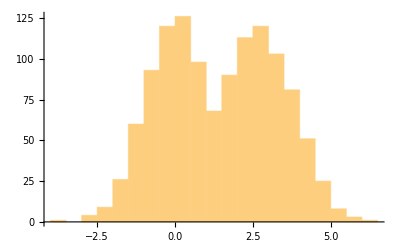

```mathematica
pp=0.5;
dim=1200;
aa1=3;
aa2=0;
ss1=1;
ss2=1;
num1=RandomVariate[NormalDistribution[aa1,ss1],Round[pp*dim]]; 
num2=RandomVariate[NormalDistribution[aa2,ss2],Round[(1-pp)*dim]]; 
num=Union[num1,num2];
Length[num];
Histogram[num,20]
```

```mathematica
Export["Test_data3.csv",num]
```

Test_data3.csv